# Приближаване на производни на функция на една променлива Оценка на грешката. Полином на Тейлър.

## Оценка на грешката. Полином на Тейлър.

### Формули за числено диференциаране

f'(t) ≈ (f(t+h) - f(t))/h - Формула с разлика напред

f'(t) ≈ (f(t) - f(t-h))/h - Формула с разлика назад

f'(t) ≈ (f(t+h) - f(t-h))/(2h)- Формула с централна разлика

## Задача 1

Да се приближи производната на функцията f(x)=e^x в интервала [0,10], като се използват трите формули за числено диференциране при h=0.5, h=0.001, h=10^-15.
Да се начертае графика на всяко едно от приближенията  заедно с графиката на производната в една координатна система.

3.52681

2.13912

2.83297

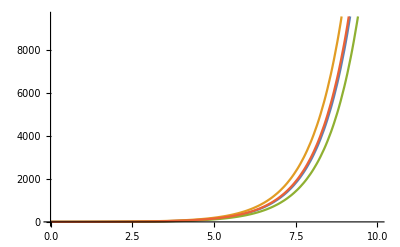

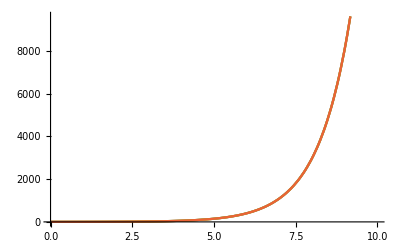

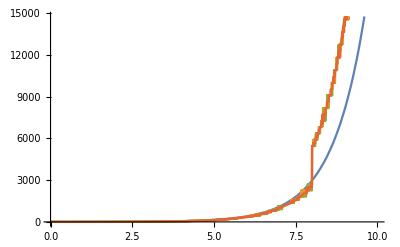

```mathematica
f[x_]:= E^x


forwardDiff[x_, h_, f_] := (f[x+h] - f[x]) / h

forwardDiff[1, 0.5, f]

backwardDiff[x_, h_, f_] := (f[x] - f[x-h]) / h

backwardDiff[1, 0.5, f]

centerwardDiff[x_, h_, f_] := (f[x+h] - f[x-h]) / (2*h)

centerwardDiff[1, 0.5, f]


Plot[{f'[x], forwardDiff[x, 0.5, f], backwardDiff[x, 0.5, f], centerwardDiff[x, 0.5, f]},{x,0,10}]

Plot[{f'[x], forwardDiff[x, 0.001, f], backwardDiff[x, 0.001, f], centerwardDiff[x, 0.001, f]},{x,0,10}]

Plot[{f'[x], forwardDiff[x,10^(-15), f], backwardDiff[x, 10^(-15), f], centerwardDiff[x, 10^(-15), f]},{x,0,10}]
```

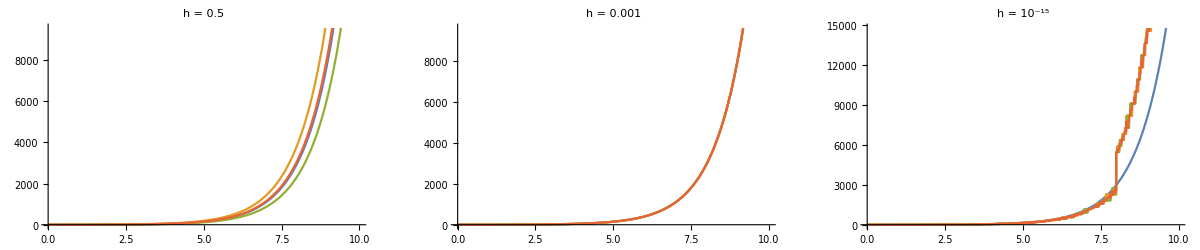

```mathematica
GraphicsRow[{Plot[{f'[x], forwardDiff[x, 0.5, f], backwardDiff[x, 0.5, f], centerwardDiff[x, 0.5, f]},{x,0,10}, PlotLabel->"h = 0.5"],

Plot[{f'[x], forwardDiff[x, 0.001, f], backwardDiff[x, 0.001, f], centerwardDiff[x, 0.001, f]},{x,0,10},PlotLabel->"h = 0.001"],

Plot[{f'[x], forwardDiff[x,10^(-15), f], backwardDiff[x, 10^(-15), f], centerwardDiff[x, 10^(-15), f]},{x,0,10},PlotLabel->"h = 10^-15"]}]
```

## Задача 2

Да се пресметнат абсолютните и относителните грешки от апроксимациите, направени в Задача 1. Да се начертаят графиките им.

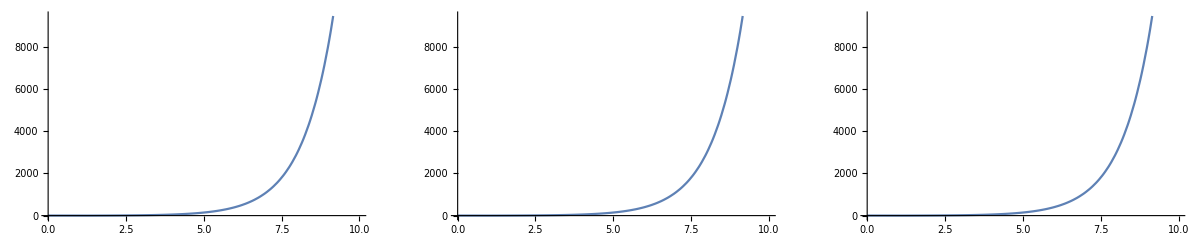

```mathematica
(* Plot[Abs[f'[x] - forwardDiff[1, 0.5, f]], {x,0,10}] *)

GraphicsRow[{Plot[Abs[f'[x] - forwardDiff[1, 0.5, f]], {x,0,10}],
Plot[Abs[f'[x] - forwardDiff[1, 0.001, f]], {x,0,10}],
Plot[Abs[f'[x] - forwardDiff[1, 10^-15, f]], {x,0,10}]}]
(*
GraphicsRow[{Plot[Abs[f'[x] - backwardDiff[1, 0.5, f]], {x,0,10}],
Plot[Abs[f'[x] - backwardDiff[1, 0.001, f]], {x,0,10}],
Plot[Abs[f'[x] - backwardDiff[1, 10^-15, f]], {x,0,10}]}]

GraphicsRow[{Plot[Abs[f'[x] - centerwardDiff[1, 0.5, f]], {x,0,10}],
Plot[Abs[f'[x] - centerwardDiff[1, 0.001, f]], {x,0,10}],
Plot[Abs[f'[x] - centerwardDiff[1, 10^-15, f]], {x,0,10}]}]
*)
(* 

absForwErr = f' - forwardDiff[1, 0.5, f]


absBackErr = f' - backwardDiff[1, 0.5, f]


absCenterErr = f' - centerwardDiff[1, 0.5, f]

Plot[Abs[f[x] - forwardDiff[x, 0.5, f]]/f[x], {x, 0, 10}]

Plot[Abs[f[x] - forwardDiff[x, 0.001, f]]/f[x], {x, 0, 10}]

*) 
(* absolute error with forward move 

absErorr[exact_, approx_, x_, h_] : = exact[x] - approx[x,h,exact]

absErorr[]


GraphicsRow[{Plot[{f'[x], forwardDiff[x, 0.5, f], backwardDiff[x, 0.5, f], centerwardDiff[x, 0.5, f]},{x,0,10}, PlotLabel->"h = 0.5"],

Plot[{f'[x], forwardDiff[x, 0.001, f], backwardDiff[x, 0.001, f], centerwardDiff[x, 0.001, f]},{x,0,10},PlotLabel->"h = 0.001"],

Plot[{f'[x], forwardDiff[x,10^(-15), f], backwardDiff[x, 10^(-15), f], centerwardDiff[x, 10^(-15), f]},{x,0,10},PlotLabel->"h = 10^-15"]}]

*)
```

## Задача 3

Да се приближи функцията x sin(x) cos(x) в интервала [0,10], като се използва полином на Тейлър от степен 2, 3, 4 около т. x_0=5. Да се начертаят графиките на функцията и приближенията и в една координатна система.

### Полином на Тейлър

f(x) ≈f(x_0) + f'(x_0)(x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+(f'''(x_0))/(3!)(x-x_0)^3+ ... +(f^(n)(x_0))/(n!)(x-x_0)^n

## Задача 3*

Коя е минималната степен на полином на Тейлър около x=5, при която абсолютната грешка по модул при приближаването на x sin(x) cos(x) във всяка точка от интервала [0,10] е по-малка от 0.1?